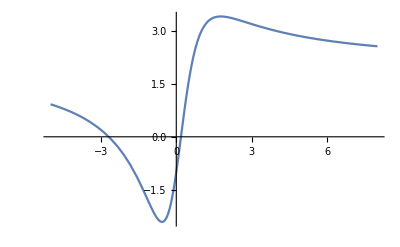

{(2+√34+2/25 (3+√34)^2)/(1+1/25 (3+√34)^2),{x→1/5 (3+√34)}}

{3.41548,{x→1.76619}}

{3.41548,{x→1.76619}}

```mathematica
(* Екстремуми на функци на една променлива *)
f[x_]:=(2 x^2+5 x-1)/(x^2+1)
Plot[f[x],{x,-5,8}]
Maximize[f[x],x]
Maximize[f[x],x]//N
NMaximize[f[x],x]
```

{3.41548,{x→1.76619}}

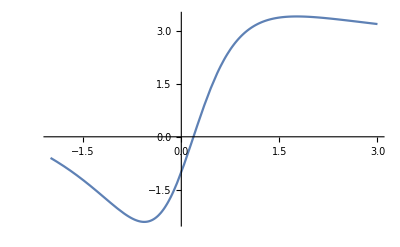

```mathematica
NMaximize[{f[x],-2≤x≤3},x]
Plot[f[x],{x,-2,3}]
```

```mathematica
NMinimize[{f[x],-2≤x≤3},x,WorkingPrecision->20]
Plot[f[x],{x,-2,3}]
```

{-2.4154759474226502354,{x→-0.56619037901930603944}}

-Graphics-

```mathematica
z=NMinimize[{f[x],-2≤x≤3},x]
Subscript[x, min]=x/.Last[z];
Subscript[f, min]=First[z];
Print["x_min=",Subscript[x, min] ",   f_min=",Subscript[f, min]]
```

{-2.41548,{x→-0.56619}}

x_min=-0.56619 ,   f_min=-2.41548

```mathematica
Clear[f];
```

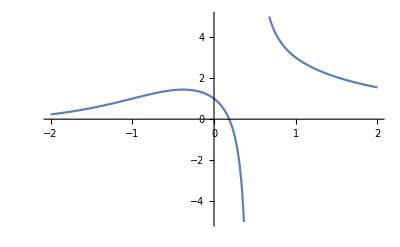

{0,0}

Minimize::natt: The minimum is not attained at any point satisfying the given constraints.

{-∞,{x→Root0.453Root[-1+2 #1+#1^3&,1]0.45339765151640377}}

{1.54545,{x→2.}}

1.54545

2.

```mathematica
f[x_]:=(2 x^2+5 x-1)/(x^3+2 x-1);
Plot[f[x],{x,-2,2},PlotRange->{-5,5}]
{Limit[f[x],x->-∞],Limit[f[x],x->∞]}
Minimize[f[x],x]
Minimize[{f[x],0.6≤x≤2},x]
MinValue[{f[x],0.6≤x≤2},x]
ArgMin[{f[x],0.6≤x≤2},x]
```

```mathematica
Subscript[x, 0]=ArgMin[f[x],x];
Subscript[f, 0]=MinValue[f[x],x];
Print["x_min=",Subscript[x, 0],",   f_min=",Subscript[f, 0]]
```

ArgMin::natt: The minimum is not attained at any point satisfying the given constraints.

x_min=Root0.453Root[-1+2 #1+#1^3&,1]0.45339765151640377,   f_min=-∞

```mathematica
Subscript[x, 0]=NArgMin[f[x],x];
Subscript[f, 0]=NMinValue[f[x],x];
Print["x_min=",Subscript[x, 0],",   f_min=",Subscript[f, 0]]
```

NArgMin::cvdiv: Failed to converge to a solution. The function may be unbounded.

NMinValue::cvdiv: Failed to converge to a solution. The function may be unbounded.

x_min=0.453398,   f_min=-1.09929×10^16

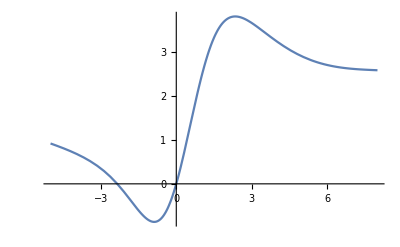

{(5 Root2.34Root[{-5-4 Cos[#1]+Cos[#1]^2+Sin[#1]^2-4 #1-4 Cos[#1] #1-7 Sin[#1] #1+5 #1^2+Cos[#1] #1^2-2 Sin[#1] #1^2&,2.3442085998622341512}]2.344208599862234+2 (Root2.34Root[{-5-4 Cos[#1]+Cos[#1]^2+Sin[#1]^2-4 #1-4 Cos[#1] #1-7 Sin[#1] #1+5 #1^2+Cos[#1] #1^2-2 Sin[#1] #1^2&,2.3442085998622341512}]2.344208599862234)^2-Sin[Root2.34Root[{-5-4 Cos[#1]+Cos[#1]^2+Sin[#1]^2-4 #1-4 Cos[#1] #1-7 Sin[#1] #1+5 #1^2+Cos[#1] #1^2-2 Sin[#1] #1^2&,2.3442085998622341512}]2.344208599862234])/(1+Cos[Root2.34Root[{-5-4 Cos[#1]+Cos[#1]^2+Sin[#1]^2-4 #1-4 Cos[#1] #1-7 Sin[#1] #1+5 #1^2+Cos[#1] #1^2-2 Sin[#1] #1^2&,2.3442085998622341512}]2.344208599862234]+(Root2.34Root[{-5-4 Cos[#1]+Cos[#1]^2+Sin[#1]^2-4 #1-4 Cos[#1] #1-7 Sin[#1] #1+5 #1^2+Cos[#1] #1^2-2 Sin[#1] #1^2&,2.3442085998622341512}]2.344208599862234)^2),{x→Root2.34Root[{-5-4 Cos[#1]+Cos[#1]^2+Sin[#1]^2-4 #1-4 Cos[#1] #1-7 Sin[#1] #1+5 #1^2+Cos[#1] #1^2-2 Sin[#1] #1^2&,2.3442085998622341512}]2.344208599862234}}

{3.79458,{x→2.34421}}

{3.79458,{x→2.34421}}

```mathematica
g[x_]:=(2 x^2+5 x-Sin[x])/(x^2+Cos[x]+1);
Plot[g[x],{x,-5,8}]
Maximize[g[x],x]
Maximize[g[x],x]//N
NMaximize[g[x],x]
```

```mathematica
Subscript[x, 0]=NArgMax[g[x],x];
Subscript[g, 0]=NMaxValue[g[x],x];
Print["x_max=",Subscript[x, 0],",   g_max=",Subscript[g, 0]]
```

x_max=2.34421,   g_max=3.79458

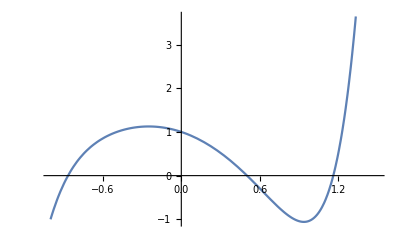

{1.12494,{x→-0.249577}}

```mathematica
f[x_]:=x^7-2 x^2-x+1
Plot[f[x],{x,-1,1.5}]
FindMaximum[f[x],{x,0.5}]
```

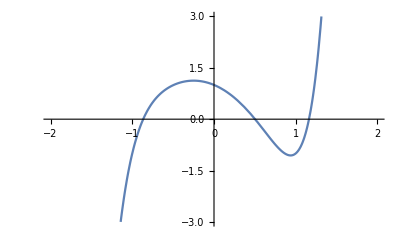

{-1.05881,{x→0.937404}}

```mathematica
f[x_]:=x^7-2 x^2-x+1
Plot[f[x],{x,-2,2},PlotRange->3]
FindMinimum[f[x],{x,1}]
```

{2.0069,-1.48659}

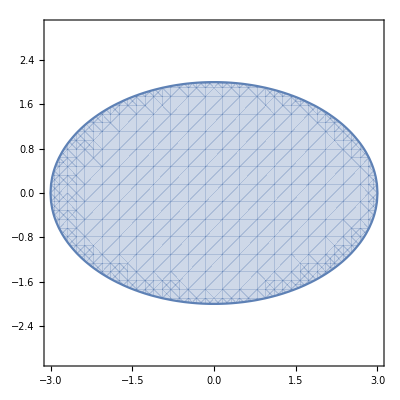

```mathematica
(* Екстремуми на функция на много променливи *)
ClearAll[z];
z[x_,y_]:=3 x-5 y
NArgMax[{z[x,y],x^2/9+y^2/4≤1},{x,y}]
RegionPlot[x^2/9+y^2/4≤1,{x,-3,3},{y,-3,3}]
```

```mathematica
Ω=ImplicitRegion[x^2/9+y^2/4≤1,{x,y}];
RegionPlot[Ω,AspectRatio->Automatic]
```

-Graphics-

```mathematica
Ω=ImplicitRegion[x^2/9+y^2/4≤1&&1≤x^2+y^2,{x,y}];
RegionPlot[Ω,AspectRatio->Automatic]
```

-Graphics-

```mathematica
ClearAll[z];
z[x_,y_]:=3 x-5 y
(* z[x_,y_]:=3 x^2-5 Cos[x y]+ArcTan[x-2 y] *)
Ω=ImplicitRegion[x^2/9+y^2/4≤1&&1≤x^2+y^2,{x,y}];
NArgMax[z[x,y],{x,y}∈Ω]
NMaxValue[z[x,y],{x,y}∈Ω]
```

{2.00689,-1.48659}

13.4536

```mathematica
(* Линейно оптимиране *)
Minimize[{2 x+3 y,5 x-2 y≥5,-2 x+3 y≥9,x≥0,y≥0},{x,y}]
```

{21,{x→3,y→5}}

```mathematica
ClearAll[z];
v={2,3};
z[x_,y_]:=v[[1]] x+v[[2]] y
Ω=ImplicitRegion[{-3 x+4 y≤12,5 x-2 y≤8,x+y≤4,2 x+4 y≥2,x≥0,y≥0},{x,y}];
Show[RegionPlot[Ω],Graphics[{Red,Arrow[{{0,0},v}]}],Plot[(72/7-v[[2]] x)/v[[1]],{x,0.5,2.5},PlotStyle->{Black;Dashed}]]
Maximize[z[x,y],{x,y}∈Ω]
```

-Graphics-

{80/7,{x→4/7,y→24/7}}

```mathematica
Maximize[{2 Subscript[x, 1]+9 Subscript[x, 2]+Subscript[x, 3]+Subscript[x, 4]-Subscript[x, 5],Subscript[x, 1]+2 Subscript[x, 2]+3 Subscript[x, 4]==8,4 Subscript[x, 2]+2 Subscript[x, 4]+Subscript[x, 5]==28,5 Subscript[x, 2]+Subscript[x, 3]+4 Subscript[x, 4]==30,Subscript[x, 1]≥0,Subscript[x, 2]≥0,Subscript[x, 3]≥0,Subscript[x, 4]≥0,Subscript[x, 5]≥0},{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5]}]
```

{34,{x_1→0,x_2→4,x_3→10,x_4→0,x_5→12}}

```mathematica
Minimize[{2 Subscript[x, 1]+5 Subscript[x, 2]+6 Subscript[x, 3]+4 Subscript[x, 4]+3 Subscript[x, 5]+Subscript[x, 6],4 Subscript[x, 1]+2 Subscript[x, 4]-2 Subscript[x, 5]+Subscript[x, 6]==12,3 Subscript[x, 1]+Subscript[x, 2]+2 Subscript[x, 4]-4 Subscript[x, 5]==15,2 Subscript[x, 1]+Subscript[x, 3]-2 Subscript[x, 4]+Subscript[x, 5]==10. Subscript[x, 1]≥0,Subscript[x, 2]≥0,Subscript[x, 3]≥0,Subscript[x, 4]≥0,Subscript[x, 5]≥0,Subscript[x, 6]≥0},{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}]
```

{87.,{x_1→0.,x_2→15.,x_3→0.,x_4→0.,x_5→0.,x_6→12.}}

```mathematica
ClearAll[f,v,x,y,z];
v={2,3,1};
f[x_,y_,z_]:=v[[1]] x+v[[2]] y+v[[3]] z
Ω=ImplicitRegion[{-3 x+4 y+z≤12,5 x-2  y-z≤8,x+y+2 z≤4,2 x+4 y≥2,x≥0,y≥0,z≥0},{x,y,z}];
Show[RegionPlot3D[Ω,Axes->True],Graphics3D[{Red,Arrow[{{0,0,0},v}]}],
Plot3D[(11.5-v[[1]] x-v[[2]] y)/v[[3]],{x,0.5,2.5},{y,0.5,2.5},PlotStyle->{Gray;Dashed}]]
Maximize[f[x,y,z],{x,y,z}∈Ω]
```

-Graphics3D-

{80/7,{x→4/7,y→24/7,z→0}}

```mathematica
(* Интегриране на функция н една променлива *)
Integrate[x^2 Cos[5 x],x]
```

2/25 x Cos[5 x]+1/125 (-2+25 x^2) Sin[5 x]

```mathematica
∫(a x^2-2 p x+3) Cos[x]ⅆx
```

-2 p Cos[x]+2 a x Cos[x]+3 Sin[x]-2 p x Sin[x]+a (-2+x^2) Sin[x]

```mathematica
∫Cos[x]ⅆx
```

Sin[x]

```mathematica
∫Exp[x]/x ⅆx
```

ExpIntegralEi[x]

```mathematica
Integrate[Cos[x],{x,0,π/3}]
```

(√3)/2

```mathematica
f[x_]:=3 x^2-x/4+π
Integrate[f[x],{x,-1,3}]
```

27+4 π

```mathematica
f[x_]:=a x^2-x/4+b
Integrate[f[x],{x,-1,3}]
```

-1+(28 a)/3+4 b

```mathematica
Integrate[1/(x^2+a),x,Assumptions->a<0]
```

ArcTan[x/(√a)]/(√a)

```mathematica
Integrate[x^a,{x,0,1},Assumptions->a<0]
```

ConditionalExpression[1/(1+a),a>-1]

```mathematica
Integrate[(x^3-2 x+1) Exp[-2 x],{x,0,1}]
```

3/8-11/(8 ⅇ^2)

```mathematica
f[x_]:=Sin[x]/x
NIntegrate[f[x],{x,-1,3},WorkingPrecision->30]
```

2.79473559836665127133908356494

```mathematica
f[x_]:=(Log[x]-x^2 ArcTan[x])/(ⅇ^(2 x)+(Cos[x])^2+1)
NIntegrate[f[x],{x,1,2},WorkingPrecision->20]
```

-0.082867787954726626838

```mathematica
∫_0^∞ ⅇ^-x (x^2-3 x+5)ⅆx
```

4

```mathematica
∫ⅇ^(-x^2)ⅆx
```

1/2 √π Erf[x]

```mathematica
∫_(-∞)^∞ ⅇ^(-x^2)ⅆx
```

√π

```mathematica
∫_(-∞)^∞ ⅇ^(-x^2) (x^2-3 x+5)ⅆx
```

(11 √π)/2

```mathematica
(* Интегриране на функция на няколко проминливи *)
Integrate[4 x^2+2 Exp[x] Sin[y],{x,0,1},{y,0,x}]
```

-ⅇ (-2+Cos[1]+Sin[1])

```mathematica
∫_0^1 ∫_0^x (4 x^2+2 Exp[x] Sin[y])ⅆyⅆx
```

-ⅇ (-2+Cos[1]+Sin[1])

```mathematica
Integrate[4 x^2+2 Exp[x] Sin[y],{x,0,1},{y,0,x}]//N
```

1.68051

```mathematica
N[Integrate[4 x^2+2 Exp[x] Sin[y],{x,0,1},{y,0,x}],20]
```

1.6805144298233629224

```mathematica
NIntegrate[4 x^2+2 Exp[x] Sin[y],{x,0,1},{y,0,x},WorkingPrecision->20]
```

1.680514429823548807

```mathematica
Ω=ImplicitRegion[0≤x≤1&&0≤y≤x,{x,y}];
Integrate[4 x^2+2 Exp[x] Sin[y],{x,y}∈Ω]
```

-ⅇ (-2+Cos[1]+Sin[1])

```mathematica
(*Ω=ImplicitRegion[x^2/9+y^2/4≤1&&1≤x^2+y^2&&2 x-3 y≤5,{x,y}];
RegionPlot[Ω,AspectRatio->Automatic]
f[x_,y_]:=4 x^2+2 Exp[x] Sin[y]
Integrate[f[x,y],{x,y}∈Ω]*)
```

```mathematica
Ω=ImplicitRegion[x^2/9+y^2/4≤1&&1≤x^2+y^2&&2 x-3 y≤5,{x,y}];
RegionPlot[Ω,AspectRatio->Automatic]
f[x_,y_]:=4 x^2+2 Exp[x] Sin[y]
NIntegrate[f[x,y],{x,y}∈Ω,WorkingPrecision->20]
```

-Graphics-

152.04925154920144884

```mathematica
Integrate[Boole[x^2+y^2≤1],{x,-1,1},{y,-1,1}]
```

π

```mathematica
NIntegrate[(x^3 Sin[2 y]+2 Cos[x+y]) Boole[x^2+y^2≤1],{x,-1,1},{y,-1,1}]
```

4.83797

```mathematica
Ω=ImplicitRegion[x^2+y^2≤1,{x,y}];
Integrate[1,{x,y}∈Ω]
```

π

```mathematica
Ω=ImplicitRegion[0≤x<∞,x];
Integrate[Boole[Sin[x]>1/2]Exp[-x],x∈Ω]
```

{ⅇ^(7 π/6)/(1+ⅇ^(2 π/3)+ⅇ^(4 π/3))}